### Definition

```mathematica
(*Shared random onsite potential generator *)
generateG[t_,W_,K_]:=RandomReal[{ W- t, W+ t},K];
(*generateG[t_,W_,K_]:=RandomReal[{-2W-0t/2,2W+0t/2},K];*)

(*ml matrix:tridiagonal with random onsite+constant hopping*)
makeML[t_,W_,K_]:=Module[{g,Ox},g=generateG[t,W,K];
Ox=ConstantArray[0,{K,K}];
Do[Ox[[i,i]]=g[[i]],{i,1,K}];
Do[Ox[[i+1,i]]=t;Ox[[i,i+1]]=t,{i,1,K-1}];
Rationalize[Ox,Power[10,-20]]];

(*mnl matrix:exponential decay hopping+random onsite*)
makeMNL[t_,W_,K_,l_,c_]:=Module[{g,Ox},g=generateG[t,W,K];
Ox=Table[l/c^Abs[i-j],{i,1,K},{j,1,K}];
Do[Ox[[i,i]]=g[[i]],{i,1,K}];
Rationalize[Ox,Power[10,-20]]];

(*mpet matrix:modified Petersen graph adjacency+random onsite+exponential decay*)
makeMPET[t_,W_,K_,l_,c_]:=Module[{g,mat,p},g=generateG[t,W,K];
p=PetersenGraph[K/2,K/4];
mat=WeightedAdjacencyMatrix[p];
Do[mat[[i,i]]=g[[i]],{i,1,K}];
Do[Do[If[i=!=j,mat[[i,j]]=l*mat[[i,j]]/c^Abs[i-j]],{j,1,K}],{i,1,K}];
Normal[Rationalize[mat,Power[10,-20]]]];
(*Module to compute neutrino masses and mixing matrices*)NeutrinoLocalMass[t_,W_,K_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,hamr,yukr},vr=Rationalize[v,Power[10,-pr]];
hamr =Rationalize[ham,Power[10,-pr]]; 
yukr =Rationalize[yuk,Power[10,-pr]]; 
ml1=makeML[t,W,K];ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];ml5=makeML[t,W,K];ml6=makeML[t,W,K];
 TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoNonLocalMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]]; ml1=makeMNL[t,W,K,l,c];ml2=makeMNL[t,W,K,l,c];ml3=makeMNL[t,W,K,l,c];ml4=makeMNL[t,W,K,l,c];ml5=makeMNL[t,W,K,l,c];ml6=makeMNL[t,W,K,l,c];TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoPetMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];ml1=makeMPET[t,W,K,l,c];ml2=makeMPET[t,W,K,l,c];ml3=makeMPET[t,W,K,l,c];ml4=makeMPET[t,W,K,l,c];ml5=makeMPET[t,W,K,l,c];ml6=makeMPET[t,W,K,l,c];TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoLocalMajoranaMass[t_,W_,K_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];Wr=Rationalize[W,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]]; ml1=makeML[t,W,K];ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];ml5=makeML[t,W,K];ml6=makeML[t,W,K];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoNonLocalMajoranaMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];Wr=Rationalize[W,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];ml1=makeMNL[t,W,K,l,c];ml2=makeMNL[t,W,K,l,c];ml3=makeMNL[t,W,K,l,c];ml4=makeMNL[t,W,K,l,c];ml5=makeMNL[t,W,K,l,c];ml6=makeMNL[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)NeutrinoPetMajoranaMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];Wr=Rationalize[W,Power[10,-pr]];hamr =Rationalize[ham,Power[10,-pr]];yukr =Rationalize[yuk,Power[10,-pr]];ml1=makeMPET[t,W,K,l,c];ml2=makeMPET[t,W,K,l,c];ml3=makeMPET[t,W,K,l,c];ml4=makeMPET[t,W,K,l,c];ml5=makeMPET[t,W,K,l,c];ml6=makeMPET[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox = Table[0,{i,1,3K},{j,1,3K}]; a1 = Table[0,{i,1,2K*3}];
a2 = Table[0,{i,1,2K*3}];
a3 = Table[0,{i,1,2K*3}];
ac = {a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];Mm = {{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1 =ArrayFlatten[Mm];Mm2 = Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];Mn = Join[Mm2,{ar1},{ar2},{ar3}] ;
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
 i=1;While[i<2K*3+4,Mma[[1,3+i]]=vr*R1[[i]];Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS = Table[0,{i,1,3},{j,1,3}];i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++] ;
{masses,PMNS}]
```

### Definition- Hopping

```mathematica
(*Shared random onsite potential generator*)generateG[t_,W_]:=RandomReal[{-t,t}];

(*ml matrix:tridiagonal with random onsite+constant hopping*)
makeML[t_,W_,K_]:=Module[{Ox},Ox=ConstantArray[0,{K,K}];
Do[Ox[[i,i]]=W,{i,1,K}];
Do[Ox[[i+1,i]]=generateG[t,W];
Ox[[i,i+1]]=generateG[t,W],{i,1,K-1}];
Ox=(Ox+Transpose[Ox])/2;
Rationalize[Ox,Power[10,-20]]];

(*mnl matrix:exponential decay hopping+random onsite*)
makeMNL[t_,W_,K_,l_,c_]:=Module[{Ox},Ox=Table[generateG[t,W]/c^Abs[i-j],{i,1,K},{j,1,K}];
Ox=(Ox+Transpose[Ox])/2;
Do[Ox[[i,i]]=W,{i,1,K}];
Rationalize[Ox,Power[10,-20]]];

(*mpet matrix:modified Petersen graph adjacency+random onsite+exponential decay*)
makeMPET[t_,W_,K_,l_,c_]:=Module[{mat,p},p=PetersenGraph[K/2,K/4];
mat=WeightedAdjacencyMatrix[p];
Do[mat[[i,i]]=W,{i,1,K}];
Do[Do[If[i=!=j,mat[[i,j]]=generateG[t,W]*mat[[i,j]]/c^Abs[i-j]],{j,1,K}],{i,1,K}];mat=(mat+Transpose[mat])/2;
Normal[Rationalize[mat,Power[10,-20]]]];
(*Module to compute neutrino masses and mixing matrices*)
NeutrinoLocalMass[t_,W_,K_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];
hamr=Rationalize[ham,Power[10,-pr]];
yukr=Rationalize[yuk,Power[10,-pr]];ml1=makeML[t,W,K];
ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];
ml5=makeML[t,W,K];ml6=makeML[t,W,K];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];
L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];
R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
i=1;
While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];
Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];
Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];
Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS=Table[0,{i,1,3},{j,1,3}];
i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++];
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)
NeutrinoNonLocalMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];
hamr=Rationalize[ham,Power[10,-pr]];
yukr=Rationalize[yuk,Power[10,-pr]];
ml1=makeMNL[t,W,K,l,c];ml2=makeMNL[t,W,K,l,c];
ml3=makeMNL[t,W,K,l,c];ml4=makeMNL[t,W,K,l,c];
ml5=makeMNL[t,W,K,l,c];ml6=makeMNL[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];
L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];
R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
i=1;
While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];
Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];
Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];
Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS=Table[0,{i,1,3},{j,1,3}];
i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++];
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)
NeutrinoPetMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,Lmix,mass,Rmix,masses,vr,yukr,hamr},vr=Rationalize[v,Power[10,-pr]];
hamr=Rationalize[ham,Power[10,-pr]];
yukr=Rationalize[yuk,Power[10,-pr]];
ml1=makeMPET[t,W,K,l,c];ml2=makeMPET[t,W,K,l,c];
ml3=makeMPET[t,W,K,l,c];ml4=makeMPET[t,W,K,l,c];
ml5=makeMPET[t,W,K,l,c];ml6=makeMPET[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[TotalML,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];
L3=Lmat[[3 K]];R1=Rmat[[1]];R2=Rmat[[1+K]];
R3=Rmat[[1+2 K]];
Mma=Table[0,{i,1,3 K+3},{j,1,3 K+3}];
i=1;While[i<=3 K,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
i=1;
While[i<=3 K,Mma[[1,3+i]]=vr*R1[[i]];
Mma[[3+i,1]]=vr*L1[[i]]*yukr[[1,1]]+vr*L2[[i]]*yukr[[1,2]]+vr*L3[[i]]*yukr[[1,3]];Mma[[2,3+i]]=vr*R2[[i]];
Mma[[3+i,2]]=vr*L1[[i]]*yukr[[2,1]]+vr*L2[[i]]*yukr[[2,2]]+vr*L3[[i]]*yukr[[2,3]];Mma[[3,3+i]]=vr*R3[[i]];
Mma[[3+i,3]]=vr*L1[[i]]*yukr[[3,1]]+vr*L2[[i]]*yukr[[3,2]]+vr*L3[[i]]*yukr[[3,3]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS=Table[0,{i,1,3},{j,1,3}];
i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Lmix[[j,-4+i]]};j++]};
i++];
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)
NeutrinoLocalMajoranaMass[t_,W_,K_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];
hamr=Rationalize[ham,Power[10,-pr]];
Wr=Rationalize[W,Power[10,-pr]];
yukr=Rationalize[yuk,Power[10,-pr]];ml1=makeML[t,W,K];
ml2=makeML[t,W,K];ml3=makeML[t,W,K];ml4=makeML[t,W,K];
ml5=makeML[t,W,K];ml6=makeML[t,W,K];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox=Table[0,{i,1,3 K},{j,1,3 K}];
a1=Table[0,{i,1,2 K*3}];
a2=Table[0,{i,1,2 K*3}];
a3=Table[0,{i,1,2 K*3}];
ac={a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];
Mm={{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1=ArrayFlatten[Mm];
Mm2=Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];
Mn=Join[Mm2,{ar1},{ar2},{ar3}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];
L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];
R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2 K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
i=1;
While[i<2 K*3+4,Mma[[1,3+i]]=vr*R1[[i]];
Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];
Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];
Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS=Table[0,{i,1,3},{j,1,3}];
i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++];
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)
NeutrinoNonLocalMajoranaMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];
hamr=Rationalize[ham,Power[10,-pr]];
Wr=Rationalize[W,Power[10,-pr]];
yukr=Rationalize[yuk,Power[10,-pr]];
ml1=makeMNL[t,W,K,l,c];ml2=makeMNL[t,W,K,l,c];
ml3=makeMNL[t,W,K,l,c];ml4=makeMNL[t,W,K,l,c];
ml5=makeMNL[t,W,K,l,c];ml6=makeMNL[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox=Table[0,{i,1,3 K},{j,1,3 K}];
a1=Table[0,{i,1,2 K*3}];
a2=Table[0,{i,1,2 K*3}];
a3=Table[0,{i,1,2 K*3}];
ac={a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];
Mm={{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1=ArrayFlatten[Mm];
Mm2=Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];
Mn=Join[Mm2,{ar1},{ar2},{ar3}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];
L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];
R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2 K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
i=1;
While[i<2 K*3+4,Mma[[1,3+i]]=vr*R1[[i]];
Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];
Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];
Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS=Table[0,{i,1,3},{j,1,3}];
i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++];
{masses,PMNS}]
(*Module to compute neutrino masses and mixing matrices*)
NeutrinoPetMajoranaMass[t_,W_,K_,l_,c_,ham_,yuk_,v_,pr_:30]:=Module[{ml1,ml2,ml3,ml4,ml5,ml6,TotalML,Lmat,evalue,Rmat,L1,L2,L3,R1,R2,R3,Mma,i,i1,j1,Lmix,Ox,Mm2,a1,a2,a3,ac,Mm,ar1,ar2,ar3,Mn,mass,Rmix,masses,PMNS,Mm1,vr,yukr,hamr,Wr},vr=Rationalize[v,Power[10,-pr]];
hamr=Rationalize[ham,Power[10,-pr]];
Wr=Rationalize[W,Power[10,-pr]];
yukr=Rationalize[yuk,Power[10,-pr]];
ml1=makeMPET[t,W,K,l,c];ml2=makeMPET[t,W,K,l,c];
ml3=makeMPET[t,W,K,l,c];ml4=makeMPET[t,W,K,l,c];
ml5=makeMPET[t,W,K,l,c];ml6=makeMPET[t,W,K,l,c];
TotalML=ArrayFlatten[{{hamr[[1,1]]*ml1,hamr[[1,2]]*ml2,hamr[[1,3]]*ml3},{hamr[[2,1]]*ml2,hamr[[2,2]]*ml4,hamr[[2,3]]*ml5},{hamr[[3,1]]*ml3,hamr[[3,2]]*ml5,hamr[[3,3]]*ml6}}];
Ox=Table[0,{i,1,3 K},{j,1,3 K}];
a1=Table[0,{i,1,2 K*3}];
a2=Table[0,{i,1,2 K*3}];
a3=Table[0,{i,1,2 K*3}];
ac={a1,a2,a3};i=1;
While[i<4,{ac[[i,1+K*(i-1)]]=t};i++];
Mm={{Ox,TotalML},{Transpose[TotalML],Ox}};
Mm1=ArrayFlatten[Mm];
Mm2=Transpose[Join[Mm1,{ac[[1]]},{ac[[2]]},{ac[[3]]}]];
ar1 = Append[ac[[1]],yukr[[1,1]]*Wr];AppendTo[ar1,yukr[[1,2]]*Wr];AppendTo[ar1,yukr[[1,3]]*Wr];
ar2 = Append[ac[[2]],yukr[[2,1]]*Wr];AppendTo[ar2,yukr[[2,2]]*Wr];AppendTo[ar2,yukr[[2,3]]*Wr];
ar3 = Append[ac[[3]],yukr[[3,1]]*Wr];AppendTo[ar3,yukr[[3,2]]*Wr];AppendTo[ar3,yukr[[3,3]]*Wr];
Mn=Join[Mm2,{ar1},{ar2},{ar3}];
(*Perform SVD on TotalML with specified precision*){Lmat,evalue,Rmat}=SingularValueDecomposition[SetPrecision[Mn,pr]];
(*Extract specific rows*)L1=Lmat[[K]];L2=Lmat[[2 K]];
L3=Lmat[[3 K]];R1=Rmat[[1+3*K]];R2=Rmat[[1+K+3*K]];
R3=Rmat[[1+2 K+3*K]];
Mma=Table[0,{i,1,6 K+6},{j,1,6 K+6}];
i=1;While[i<2 K*3+4,Mma[[i+3,i+3]]=evalue[[i,i]];i++];
i=1;
While[i<2 K*3+4,Mma[[1,3+i]]=vr*R1[[i]];
Mma[[3+i,1]]=vr*L1[[i]];Mma[[2,3+i]]=vr*R2[[i]];
Mma[[3+i,2]]=vr*L2[[i]];Mma[[3,3+i]]=vr*R3[[i]];
Mma[[3+i,3]]=vr*L3[[i]];i++];
{Lmix,mass,Rmix}=SingularValueDecomposition[SetPrecision[Mma,pr]];
masses=Diagonal[mass];PMNS=Table[0,{i,1,3},{j,1,3}];
i1=1;
While[i1<4,{j1=1;
While[j1<4,{PMNS[[j1,-i1]]=Lmix[[j1,-4+i1]]};j1++]};
i1++];
{masses,PMNS}]
```

### Computing

```mathematica
Quit
```

```mathematica
LaunchKernels[$ProcessorCount];
```

```mathematica
ParallelEvaluate[Get["/home/as/Documents/Wolfram_Mathematica/Codes/Anderson/Site.m"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Get["/home/as/Documents/Wolfram_Mathematica/Codes/Anderson/Site.m"]
```

```mathematica
Get["/home/as/Documents/Wolfram_Mathematica/Codes/Anderson/Hopp.m"]
```

```mathematica
t=0.5;
```

```mathematica
nt=10;t=0.10;W=05;K=12;l=t*c;c=5;v=0.173;(*strong site dirac*)
```

```mathematica
nt=10;t=0.20;W=05;K=8;l=t*c;c=3;v=0.173;(*strong site maj*)
```

```mathematica
nt=10;t=0.20;W=10;K=8;l=t*c;c=3;v=0.173;(*Hopping*)
```

```mathematica
nt=10;t=0.1;W=10;K=8;l=t*c;c=2;v=0.173;(*Hopping weak site maj*)
```

```mathematica
yuk={{0.1,0.6,0.4},{0.6,0.1,0.5},{0.4,0.5,0.1}};ham=IdentityMatrix[3];(*weaksite *)
```

```mathematica
yuk=IdentityMatrix[3];ham={{1,0.5,0.4},{0.1,01,0.5},{0.2,0.7,01}};(*weaksite*)
```

```mathematica
yuk={{0.1,0.6,0.4},{0.6,0.1,0.5},{0.4,0.5,0.1}};x=0;y=0;z=0;(*Using for hopping *)
```

```mathematica
yuk=IdentityMatrix[3];x=0.2;y=0.6;z=0.4;(*hoppping*)
```

```mathematica
yuk={{1,0.5,0.4},{0.1,01,0.5},{0.2,0.7,01}};x=0;y=0;z=0;(*local,k=9 X*)
```

```mathematica
yuk={{1,0.2,0.6},{0.2,01,0.4},{0.6,0.4,01}};x=0;y=0;z=0;(*local,k=9 - ok*)
```

NeutrinoLocalMajoranaMass(0.1,10,9,0,0,0,(1 | 0.2 | 0.6
0.2 | 1 | 0.4
0.6 | 0.4 | 1),0.173,30)

```mathematica
yuk={{1,0.2,0.2},{0.2,01,0.2},{0.2,0.2,01.}};
```

```mathematica
yuk={{01,0.4,0.6},{0.3,01,0.8},{0.9,0.3,01}};(*Yuk ss *)
```

```mathematica
yuk={{1,0.5,0.4},{0.5,01,0.3},{0.5,0.9,01}};ham = IdentityMatrix[3];(*local,k=9 - ok*)
NeutrinoLocalMajoranaMass[t,W,9,ham,yuk,v,30]
```

{{20.6651214640467128230659831949,10.4589728125082815595656718771,10.4588952572940230652243566903,10.4474012093563034897184095993,10.4471769226406260612761435698,10.4428052832922788830673807871,10.4425142741391716837221427607,10.4251906877020579023954015982,10.42504794472901867845407877,10.4037664205907251214727614349,10.4031829657890999027910324338,10.4004557609361644756961692702,10.4003544454318078782639507613,10.3130271868899887064522134195,10.3126519095534714163766779212,10.3116354767060830375556661827,10.3110408982136987678562434942,10.2959668526377336546369748756,10.2956472985305468099396723099,10.2098253014681688568011504004,10.2094863918522979821372250912,10.2081516334869216736850865793,10.2078042402329604927491839735,10.1298471580074830357032437584,10.1290888718482821826464361918,10.0612506509230014254641643852,10.0607671070665194420840437902,10.0228436364618864100316430156,10.0219522530386460482999086696,10.0196733036351635000045147429,10.018762843776640621828767978,9.98265458016147926241995601163,9.98179947240073546286513068383,9.9668100295544078667291413604,9.9663941142604258823377015907,9.9514507011118150746287978068,9.95093430826669828519362827548,9.8225570698911110600817188389,9.82224718274280025804595184332,9.81671535847284252908535893961,9.81651272174233334943018212316,9.75882821500777336641573016633,9.75865899274943284711226586691,9.7581712493942728316676236201,9.75799496267786289057912824589,9.69412467375189367622896894855,9.69406310234705597984108682081,9.67875516431846175919032282523,9.67842897638996017646525573652,9.63818376483594943191429444519,9.63817482379955463134369366722,9.59391090565099595878198613555,9.59389466846678491441236114917,9.58452978619968216460681857258,9.58450971112868108515311300077,5.89438705165534261554150019293,4.38795829501909376061996916791,7.49518121849038045795682207486×10^-17,7.33118881287370103586394195644×10^-17,7.20506638484531626765327023973×10^-17},(-1.71876834806847216902482036965×10^-6 | -1.19924781970319489938585569757×10^-6 | 0.999853140994983569374162256459
0.99985150376541939461133172313 | 6.94349286291949488351695187938×10^-6 | 1.85997441775722689029577529755×10^-6
-6.70666530354565825685806006204×10^-6 | 0.999854581433773605092825028596 | 1.25348951760443474415070435198×10^-6)}

```mathematica
yuk=IdentityMatrix[3];ham={{01,0.5,0.35},{0.12,01,0.3},{0.4,0.7,01}};(*weaksite*)
NeutrinoLocalMass[t,W,9,ham,yuk,v,30][[2]]
```

(0.0526193459444434028984976219862 | -0.885386779766093902861694226326 | 0.44589125359253586796640673026
0.901704590071024431526639526855 | 0.238276943710379382424432130976 | 0.357299347814853960802792976622
0.42736033217610702513632566977 | -0.3855877339952681604752328795 | -0.806916465783216190839570424953)

```mathematica
ham={{01,0.4,0.6},{0.3,01,0.8},{0.9,0.3,01}};(*Ham ss*)
```

```mathematica
yuk=IdentityMatrix[3];ham={{0.14,01,0.3},{01,0.5,0.35},{0.4,0.7,01}};(*weaksite*)
NeutrinoPetMass[t,W,12,l,c,ham,yuk,v,30]
```

{{19.0790986957107082158800447059,18.7970140584016879546434325421,18.6627747513460491847219620814,18.6287632147034570651617719733,18.6003970171478250306351246649,18.5198919348463532546519527362,18.1277683021825005064405493335,18.0551907695440205623425257897,18.0265156714231175448786919553,17.9983845897548223470996617975,17.9172020096204180995273179766,17.6160630889253404319671332474,7.46036303119615976885947760204,7.34916667090160338981094173664,7.28977274621842511181414464918,7.27113418997811317779957046498,7.25385357360314541902046670184,7.19747159232873054209969414594,7.06942493615673431032627740593,7.0425888775388546148913961173,7.02120514311574188413434111471,6.99717402353464340776359726944,6.98426279750175128161309258111,6.87644073959470202226842632348,5.37293272722893006887483050026,5.31210054119376140361902715762,5.29784620298305882520054784322,5.25439659504548443312422883198,5.23449607700070248386357576028,5.20666768666165201410543252604,5.142953061139504238766116144,5.08946543021694315123560749977,5.06251951970887979469363398423,5.05170190028905488085954312878,5.01696539734085920786685419807,4.94809479761830984212823264929,4.43343917562939055318914337462×10^-7,3.24300893193167102905359487666×10^-7,1.26580985249203493136676101572×10^-7},(-0.489044638543567603535310294496 | -0.861599622184216070696263268007 | -0.134165487881104681846452165624
-0.675680338480828284527796969659 | 0.471538115165129492909375907647 | -0.56619725450832196979862974279
-0.551545310417108546773742025223 | 0.18629989280145043763666153357 | 0.812593450805212472106903622061)}

```mathematica
t=0.2
W=10
```

0.2

10

```mathematica
c=2
```

2

```mathematica
c
W
t
```

1.2

5

0.2

## Single Scenario

```mathematica
$KernelCount
```

104

```mathematica
LaunchKernels[$ProcessorCount]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
DistributeDefinitions["NeutrinoLocalMass","t","W","K","l","c","ham","yuk","v"];
```

#### Dirac Case

```mathematica
nt=10;
```

```mathematica
tick=AbsoluteTime[];
Anmex1=ParallelTable[NeutrinoLocalMass[t,W,9,ham,yuk,v,30],{ii,1,nt},{jj,1,nt},{kk,1,nt}
];
AbsoluteTime[]-tick
```

14.7089

```mathematica
Anmexl=Anmex1[[All,All,All]];
```

#### Majorana Case

```mathematica
nt=5;t=0.2;W=10;K=8;l=t*c;c=7;v=0.173;
```

```mathematica
tick=AbsoluteTime[];
Anmexmaj1=ParallelTable[NeutrinoLocalMajoranaMass[t,W,K,l,c,ham,yuk,v,30],{ii,1,nt},{jj,1,nt},{kk,1,nt}];
AbsoluteTime[]-tick
```

```mathematica
Anmexl=Anmex1[[All,All,All]];
```

```mathematica
$KernelCount
```

## Multiple Scenario

#### Dirac Case

```mathematica
Clear[Anmex1];nt=15;
```

```mathematica
tick=AbsoluteTime[];
Anmexdir=ParallelTable[{NeutrinoLocalMass[t,W,K,ham,yuk,v,30],NeutrinoNonLocalMass[t,W,K,l,c,ham,yuk,v,30],NeutrinoPetMass[t,W,8,l,c,ham,yuk,v,30]},{ii,1,nt},{jj,1,nt},{kk,1,nt}];
AbsoluteTime[]-tick
```

564.42

```mathematica
Anmex1=Anmexdir;
```

```mathematica
Anmexl=Anmex1[[All,All,All,1]];
Anmexnl=Anmex1[[All,All,All,2]];
Anmexpet=Anmex1[[All,All,All,3]];
```

#### Majorana Case

```mathematica
nt=10;t=0.20;W=5;K=8;l=t*c;c=1.2;v=0.173;
```

```mathematica
yuk=IdentityMatrix[3];x=0;y=0;z=0;
```

```mathematica
yuk={{1,0.2,0.6},{0.2,1,0.4},{0.6,0.4,1}};x=0;y=0;z=0;
```

```mathematica
yuk=IdentityMatrix[3];x=0.2;y=0.6;z=0.4;
```

```mathematica
Clear[Anmex1];
```

```mathematica
tick=AbsoluteTime[];
Anmexmaj=ParallelTable[{NeutrinoLocalMajoranaMass[t,W,K,ham,yuk,v,30],NeutrinoNonLocalMajoranaMass[t,W,K,l,c,ham,yuk,v,20],NeutrinoPetMajoranaMass[t,W,8,l,c,ham,yuk,v,20]},{ii,1,nt},{jj,1,nt},{kk,1,nt}];
AbsoluteTime[]-tick
```

49738.6

```mathematica
Anmex1=Anmexmaj;
```

```mathematica
Anmexl=Anmex1[[All,All,All,1]];
Anmexnl=Anmex1[[All,All,All,2]];
Anmexpet=Anmex1[[All,All,All,3]];
```

```mathematica
Length[Anmexl]
```

10

```mathematica
Anmexl[[1,1,1]][[2]]
```

(0.49113172563375629645545814651 | -0.869784389442003613863151639879 | 0.0443332845386709362761506270804
0.311887279353839743905035929369 | 0.223174819123688924857109116948 | 0.923374281409662811354981276272
0.813152341367241159352056473602 | 0.439737138280538302803305040226 | -0.380939870229594152347237348813)

```mathematica
(*Export["/home/as/Documents/Wolfram_Mathematica/Codes/Anderson/MajMaj2.mx",Anmex1,"MX"]*)
```

#### Local

```mathematica
mat ={};mass={};
```

```mathematica
i=1;
While[i<nt+1,{j=1;
While[j<nt+1,{k=1;
While[k<nt+1,{AppendTo[mat,Anmexl[[i,j,k]][[2]]],AppendTo[mass,Anmexl[[i,j,k]][[1]][[-3;;-1]]]};k++]};j++]};i++]
```

```mathematica
mass[[1;;4]]
```

(1.52861654053586769309507880717×10^-16 | 4.42946880805119398080851393669×10^-17 | 3.20362340690840566593050751707×10^-17
1.60841313631445779623723362026×10^-16 | 4.79916242362031998592876842832×10^-17 | 3.36946430920401069138922447044×10^-17
1.5331810863483388911266282094×10^-16 | 4.27398176461589217403335081873×10^-17 | 3.32452996815493447603518650813×10^-17
1.60601406888209562788225531665×10^-16 | 4.59375045838158090200274589403×10^-17 | 3.3984373688625991966615551784×10^-17)

```mathematica
m1=mass[[All,1]];
m2=mass[[All,2]];
m3=mass[[All,3]];num=100;
```

```mathematica
medm1=Partition[m1,num];
medm2=Partition[m2,num];
medm3=Partition[m3,num];
(*Compute median of each chunk*)
median1=Median/@medm1;
median2=Median/@medm2;
median3=Median/@medm3;
```

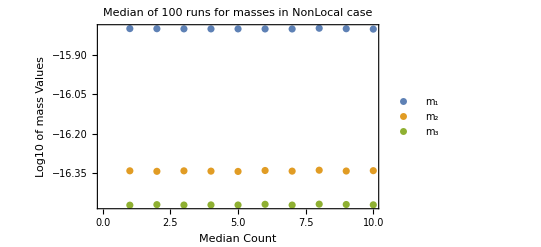

```mathematica
ListPlot[Log10[{median1,median2,median3}],Frame->True,PlotLegends->{Subscript[m,1],Subscript[m,2],Subscript[m,3]},FrameLabel->{Style["Median Count",Black,FontSize->14],(*X-axis label size*)Style["Log10 of mass Values",Black,FontSize->14]    (*Y-axis label size*)},FrameTicksStyle->Directive[Black,FontSize->14],(*Tick label size*)LabelStyle->Directive[Black],(*General label color*)PlotLabel->Style["Median of 100 runs for masses in NonLocal case",FontSize->15]]
```

```mathematica
(*ListPlot[Log10[{median1,median2,median3}],Frame->True,FrameStyle->Directive[Black],PlotMarkers->{Graphics[{Circle[]},ImageSize->5],Graphics[{Polygon[{{0,0.15},{-0.13,-0.12},{0.13,-0.12}}]},ImageSize->5],Graphics[{Polygon[{{0,0.15},{0.13,0},{0,-0.15},{-0.13,0}}]},ImageSize->5]},PlotLegends->{Subscript[m,1],Subscript[m,2],Subscript[m,3]},FrameLabel->{Style["Median Count",Black,FontSize->14],Style["Log10 of mass Values",Black,FontSize->14]},FrameTicksStyle->Directive[Black,FontSize->13],LabelStyle->Directive[Black],PlotLabel->Style["Median of 100 runs for masses in NonLocal case",FontSize->14]]*)
```

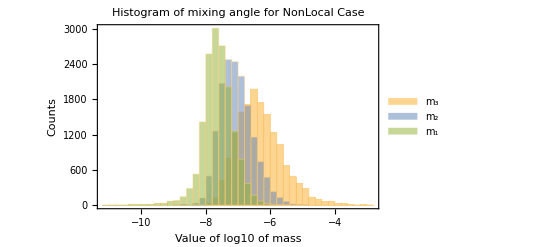

```mathematica
Histogram[Log10[{m1,m2,m3}],{0.2},ChartLegends->{"m_3","m_2","m_1"},PlotRange->{All,All},Frame->True,FrameLabel->{Style["Value of log10 of mass",Black,FontSize->14],Style["Counts",Black,FontSize->14]},LabelStyle->Black,FrameTicksStyle->Directive[Black,FontSize->13],PlotLabel->Style["Histogram of mixing angle for NonLocal Case",FontSize->15]]
```

```mathematica
mat[[1;;4]]
```

({-3.03073803269379426576079464968×10^-12,8.1573847154366250049759371813×10^-10,-0.990739975674787312197176353274} | {-0.999675732868816906376485117493,-6.80059362754002233460149739794×10^-6,0.0000112459059723095706590269561466} | {8.26270999962967613885687000526×10^-8,-0.999297401769330414403503102706,-0.0000367775129479720788679174530542}
{0.999762461770508672011734637731,-2.62664403631103149816615328931×10^-6,4.22104871608335625823874841232×10^-6} | {-1.0259464720929251156941353963×10^-6,-0.99973442314650094054127329642,-4.46009365114598272557597106268×10^-6} | {5.00071393581060345854977784759×10^-8,1.35279011695825514996113537392×10^-7,-0.999637150028683939718007744399}
{-9.56756345248338151836560973338×10^-6,-0.995155336707602701740340183981,-0.0000179931401373569805593032922193} | {-1.24485210672557208185423049039×10^-6,-6.99675410339596208821132137257×10^-6,0.999428380718281849177520753821} | {0.969418550954134869116642022758,-0.000180814776900753162521667502953,0.0000604953203555383889795096419959}
{-0.997364556869083536090165321355,0.0000523600594874956551267620776539,-0.0000127085068655346139238319889912} | {3.26511113098952884585470934258×10^-8,2.44043622255563932665064796734×10^-6,-0.998518676255299034144745601674} | {2.16737312398191397015937148968×10^-6,0.995281819759028760651666246291,0.0000393250090319379183289648904834})

```mathematica
selectedMatrices=Select[mat,AllTrue[Diagonal[#.Transpose[#]],0.99<=#<=1&]&];
count=Length[selectedMatrices]
```

8790

```mathematica
Length[mat]
```

15625

```mathematica
mat=selectedMatrices;
```

```mathematica
reorderColumns[matrix_?MatrixQ]:=Module[{transposedMatrix,reorderedColumnsList},If[Dimensions[matrix]!={3,3},Return["Error: Input must be a 3x3 matrix."],transposedMatrix=Transpose[matrix];
reorderedColumnsList=transposedMatrix[[{2,3,1}]];
Transpose[reorderedColumnsList]]]
```

```mathematica
reorderedMatList=reorderColumns/@mat;(*Inverting for IO*)
```

```mathematica
mat=reorderedMatList;
```

```mathematica
mat[[5]]
```

(-3.2607592468921068932823884563×10^-6 | 7.6236285038789265078122626396×10^-6 | -0.999211317670965444549118184606
-0.999673409329506386914006608743 | -4.82300371106087625533072601592×10^-6 | 2.27952691494196845895114803555×10^-8
-1.25986163230217962644415833311×10^-8 | 0.999635464252652389369361560154 | 1.39217520231495645902304751194×10^-10)

```mathematica
h1 = Table[Abs[mat[[i,1,1]]],{i,1,Length[mat]}];
h2 = Table[Abs[mat[[i,1,2]]],{i,1,Length[mat]}];
h3 = Table[Abs[mat[[i,1,3]]],{i,1,Length[mat]}];
h4 = Table[Abs[mat[[i,2,1]]],{i,1,Length[mat]}];
h5 = Table[Abs[mat[[i,2,2]]],{i,1,Length[mat]}];
h6 = Table[Abs[mat[[i,2,3]]],{i,1,Length[mat]}];
h7 = Table[Abs[mat[[i,3,1]]],{i,1,Length[mat]}];
h8 = Table[Abs[mat[[i,3,2]]],{i,1,Length[mat]}];
h9 = Table[Abs[mat[[i,3,3]]],{i,1,Length[mat]}];
```

```mathematica
Length[h1]
```

8790

```mathematica
th13=ArcSin[h3]/Degree;
th12 = ArcTan[h2/h1]/Degree;
th23=ConstantArray[0,Length[h6]];
Do[If[h6[[i]]==0||h9[[i]]==0,th23[[i]]=0,th23[[i]]=If[h6[[i]]<h9[[i]],h6[[i]]/h9[[i]],h9[[i]]/h6[[i]]]],{i,1,Length[h6]}];
th23=th23/Degree;(*th23= ArcSin[h6/h9]/Degree;
th13d=th13/Degree;
th13a=ArcCos[Sqrt[h1^2+h3^2]] /Degree;*)
```

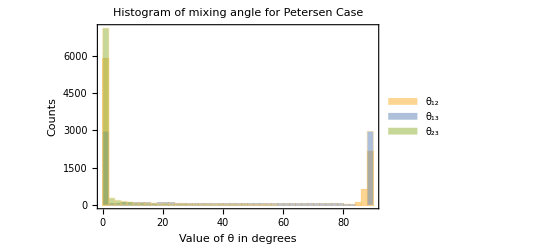

```mathematica
Histogram[Abs[{th13,th12,th23}],{02},ChartLegends->{"θ_12","θ_13","θ_23"},PlotRange->{{0,90},All},Frame->True,FrameLabel->{Style["Value of θ in degrees",Black,FontSize->14],Style["Counts",Black,FontSize->14]},LabelStyle->Black,FrameTicksStyle->Directive[Black,FontSize->14],PlotLabel->Style["Histogram of mixing angle for Petersen Case",FontSize->15]]
```

```mathematica
th23= ArcSin[h6/h9]/Degree;
```

```mathematica
ham
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
yuk
```

(1 | 0.5 | 0.4
0.5 | 1 | 0.3
0.5 | 0.9 | 1)

```mathematica
t
```

0.2

```mathematica
c
```

3

```mathematica
W
```

5

#### Non-Local

```mathematica
mat ={};mass={};
```

```mathematica
i=1;
While[i<nt+1,{j=1;
While[j<nt+1,{k=1;
While[k<nt+1,{AppendTo[mat,Anmexnl[[i,j,k]][[2]]],AppendTo[mass,Anmexnl[[i,j,k]][[1]][[-3;;-1]]]};k++]};j++]};i++]
```

```mathematica
mass[[1;;4]]
```

(3.046012296239826404×10^-7 | 4.584764203299139797×10^-10 | 7.9619418590798439091×10^-11
2.2725383488688907527×10^-8 | 5.0078934703968825496×10^-9 | 9.2595211158453640306×10^-10
2.5541552261759316405×10^-8 | 6.3861480119942103718×10^-10 | 3.5736178994086465366×10^-11
3.1589892426519460159×10^-9 | 8.4407663425820203054×10^-10 | 7.904404761228264801×10^-11)

```mathematica
m1=mass[[All,1]];
m2=mass[[All,2]];
m3=mass[[All,3]];
```

```mathematica
medm1=Partition[m1,num];
medm2=Partition[m2,num];
medm3=Partition[m3,num];
(*Compute median of each chunk*)
median1=Median/@medm1;
median2=Median/@medm2;
median3=Median/@medm3;
```

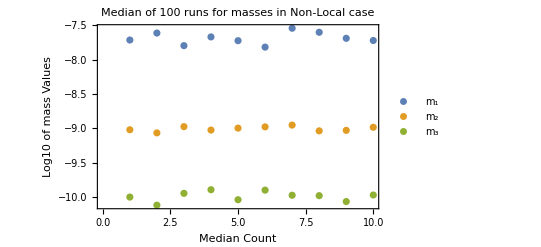

```mathematica
ListPlot[Log10[{median1,median2,median3}],Frame->True,PlotLegends->{Subscript[m, 1], Subscript[m, 2], Subscript[m, 3]},FrameLabel->{Style["Median Count",Black],Style["Log10 of mass Values",Black]},LabelStyle->Black,PlotLabel->"Median of 100 runs for masses in Non-Local case"]
```

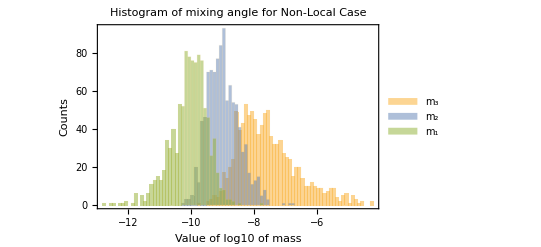

```mathematica
Histogram[Log10[{m1,m2,m3}],{0.1},ChartLegends->{"m_3","m_2","m_1"},PlotRange->{All,All},Frame->True,FrameLabel->{Style["Value of log10 of mass",Black],Style["Counts",Black]},LabelStyle->Black,PlotLabel->"Histogram of mixing angle for Non-Local Case"]
```

```mathematica
mat[[1;;4]]
```

({-0.91469550092915778894,0.28359418002946395388,-0.28771625878824889023} | {0.19378461048668193896,-0.31712328651218484082,-0.92788526590702810076} | {0.35457578882996933065,0.90490464129774412104,-0.23510304508719768484}
{0.26131114139990272205,-0.74733244722530616856,-0.60654179088515411205} | {-0.4523138030819263514,0.46021779725016880541,-0.76281733212614408888} | {0.8525244538957802123,0.47410596532055351518,-0.21862061298319262952}
{-0.57382753781795922163,0.80650261128700452658,0.14151012358091438964} | {0.78273786201520851136,0.59103712627571136467,-0.19452875582083115237} | {-0.24067519409261160471,-0.00053942578510118506855,-0.97014942485804807105}
{0.19665697510998182563,0.74812106972299742968,-0.63340919556124278341} | {-0.072804255433629826688,-0.63316966807030409133,-0.77037405433766490803} | {-0.97771581817327851692,0.19759294040774957747,-0.070059396309529605221})

```mathematica
selectedMatrices=Select[mat,AllTrue[Diagonal[#.Transpose[#]],0.90<=#<=1&]&];

count=Length[selectedMatrices]
```

937

```mathematica
Length[mat]
```

1000

```mathematica
mat=selectedMatrices;
```

```mathematica
h1 = Table[Abs[mat[[i,1,1]]],{i,1,Length[mat]}];
h2 = Table[Abs[mat[[i,1,2]]],{i,1,Length[mat]}];
h3 = Table[Abs[mat[[i,1,3]]],{i,1,Length[mat]}];
h4 = Table[Abs[mat[[i,2,1]]],{i,1,Length[mat]}];
h5 = Table[Abs[mat[[i,2,2]]],{i,1,Length[mat]}];
h6 = Table[Abs[mat[[i,2,3]]],{i,1,Length[mat]}];
h7 = Table[Abs[mat[[i,3,1]]],{i,1,Length[mat]}];
h8 = Table[Abs[mat[[i,3,2]]],{i,1,Length[mat]}];
h9 = Table[Abs[mat[[i,3,3]]],{i,1,Length[mat]}];
```

```mathematica
Length[h1]
```

1000

```mathematica
th13=ArcSin[h3]/Degree;
th12 = ArcTan[h2/h1]/Degree;
Do[If[h6[[i]]==0||h9[[i]]==0,th23[[i]]=0,th23[[i]]=If[h6[[i]]<h9[[i]],h6[[i]]/h9[[i]],h9[[i]]/h6[[i]]]],{i,1,Length[h6]}];
th23=th23/Degree;
```

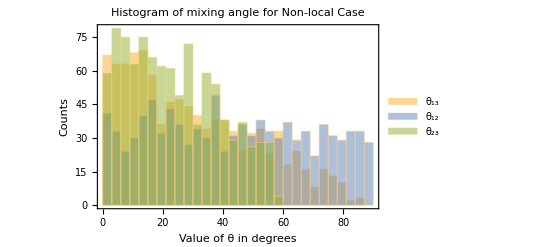

```mathematica
Histogram[Abs[{th13,th12,th23}],{03},ChartLegends->{"θ_13","θ_12","θ_23"},PlotRange->{{0,90},All},Frame->True,FrameLabel->{Style["Value of θ in degrees",Black],Style["Counts",Black]},LabelStyle->Black,PlotLabel->"Histogram of mixing angle for Non-local Case"]
```

#### Petersen

```mathematica
mat ={};mass={};
```

```mathematica
i=1;
While[i<nt+1,{j=1;
While[j<nt+1,{k=1;
While[k<nt+1,{AppendTo[mat,Anmexpet[[i,j,k]][[2]]],AppendTo[mass,Anmexpet[[i,j,k]][[1]][[-3;;-1]]]};k++]};j++]};i++]
```

```mathematica
mass[[1;;4]]
```

(6.4897226638204157445×10^-9 | 3.7584907522440363235×10^-11 | 1.6163454793053168867×10^-11
1.8805344374586502788×10^-9 | 8.4327781429013189405×10^-11 | 4.5037052096532437201×10^-12
3.2587542525251697212×10^-10 | 3.4635662645146970789×10^-11 | 2.4564547414043514331×10^-12
3.326516138368776094×10^-8 | 7.2248688028292207194×10^-11 | 8.9157559837737031318×10^-13)

```mathematica
m1=mass[[All,1]];
m2=mass[[All,2]];
m3=mass[[All,3]];
```

```mathematica
medm1=Partition[m1,num];
medm2=Partition[m2,num];
medm3=Partition[m3,num];
(*Compute median of each chunk*)
median1=Median/@medm1;
median2=Median/@medm2;
median3=Median/@medm3;
```

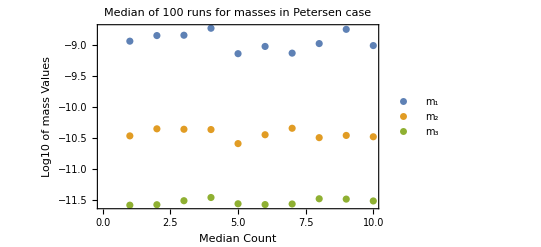

```mathematica
ListPlot[Log10[{median1,median2,median3}],Frame->True,PlotLegends->{Subscript[m, 1], Subscript[m, 2], Subscript[m, 3]},FrameLabel->{Style["Median Count",Black],Style["Log10 of mass Values",Black]},LabelStyle->Black,PlotLabel->"Median of 100 runs for masses in Petersen case"]
```

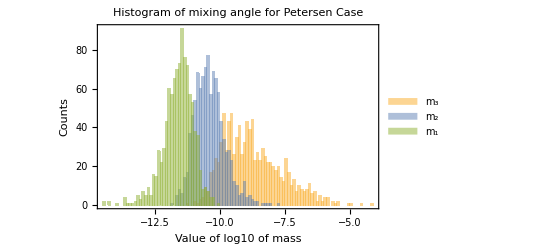

```mathematica
Histogram[Log10[{m1,m2,m3}],{0.1},ChartLegends->{"m_3","m_2","m_1"},PlotRange->{All,All},Frame->True,FrameLabel->{Style["Value of log10 of mass",Black],Style["Counts",Black]},LabelStyle->Black,PlotLabel->"Histogram of mixing angle for Petersen Case"]
```

```mathematica
mat[[1;;4]]
```

({-0.96939048947252867386,-0.14074596892208306497,0.19882735946080874188} | {-0.23054332248186712281,0.25446290819997113027,-0.93376098877644353088} | {-0.081751899739902729499,0.95645674974442952059,0.27736923386812874316}
{0.95208551918188747977,0.30532593687567244615,0.01421091019723810055} | {0.0819030031638579835,-0.21024570969813850614,-0.96993422180142809028} | {-0.29445076010020494538,0.92862015737527034111,-0.22404886913818306181}
{0.53362392125221902251,-0.78019957832477713948,0.32572037113695149787} | {-0.19926441037204178108,-0.49072848193767167086,-0.8468328443617951377} | {-0.82182673639936799713,-0.38764633093209421079,0.41676271738121914605}
{0.88472187041238641455,0.46493103915581200034,-0.031192450660609257512} | {-0.45733197921726354342,0.87913957485550929557,0.13317154730850724166} | {-0.089339516017499780274,0.10382137118912029107,-0.98984639412462943732})

```mathematica
selectedMatrices=Select[mat,AllTrue[Diagonal[#.Transpose[#]],0.90<=#<=1&]&];

count=Length[selectedMatrices]
```

922

```mathematica
Length[mat]
```

1000

```mathematica
mat=selectedMatrices;
```

```mathematica
h1 = Table[Abs[mat[[i,1,1]]],{i,1,Length[mat]}];
h2 = Table[Abs[mat[[i,1,2]]],{i,1,Length[mat]}];
h3 = Table[Abs[mat[[i,1,3]]],{i,1,Length[mat]}];
h4 = Table[Abs[mat[[i,2,1]]],{i,1,Length[mat]}];
h5 = Table[Abs[mat[[i,2,2]]],{i,1,Length[mat]}];
h6 = Table[Abs[mat[[i,2,3]]],{i,1,Length[mat]}];
h7 = Table[Abs[mat[[i,3,1]]],{i,1,Length[mat]}];
h8 = Table[Abs[mat[[i,3,2]]],{i,1,Length[mat]}];
h9 = Table[Abs[mat[[i,3,3]]],{i,1,Length[mat]}];
```

```mathematica
Length[h1]
```

1000

```mathematica
th13=ArcSin[h3]/Degree;
th12 = ArcTan[h2/h1]/Degree;
Do[If[h6[[i]]==0||h9[[i]]==0,th23[[i]]=0,th23[[i]]=If[h6[[i]]<h9[[i]],h6[[i]]/h9[[i]],h9[[i]]/h6[[i]]]],{i,1,Length[h6]}];
th23=th23/Degree;
```

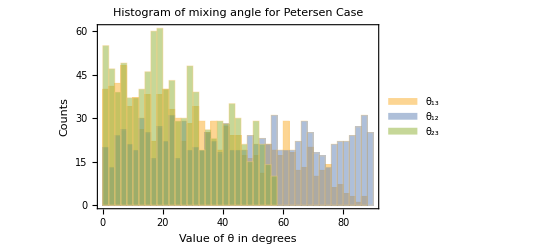

```mathematica
Histogram[Abs[{th13,th12,th23}],{2},ChartLegends->{"θ_13","θ_12","θ_23"},PlotRange->{{0,90},All},Frame->True,FrameLabel->{Style["Value of θ in degrees",Black],Style["Counts",Black]},LabelStyle->Black,PlotLabel->"Histogram of mixing angle for Petersen Case"]
```

```mathematica
Cos[th23[[1]]]
```

-0.2564257042999478

```mathematica
h6[[1]]
```

0.93376098877644353088

```mathematica
h9[[1]]
```

0.27736923386812874316

```mathematica
mat[[1]]
```

(-0.96939048947252867386 | -0.14074596892208306497 | 0.19882735946080874188
-0.23054332248186712281 | 0.25446290819997113027 | -0.93376098877644353088
-0.081751899739902729499 | 0.95645674974442952059 | 0.27736923386812874316)

## Mass

#### Dirac Case

```mathematica
nt=10;t=0.10;W=10;K=8;l=t*c;c=1.2;v=0.173;
```

```mathematica
Clear[Anmex1];nt=25;
```

```mathematica
tick=AbsoluteTime[];
Anmexdir=ParallelTable[{NeutrinoLocalMass[t,W,K,x,y,z,yuk,v,30],NeutrinoNonLocalMass[t,W,K,l,c,x,y,z,yuk,v,30],NeutrinoPetMass[t,W,8,l,c,x,y,z,yuk,v,30]},{ii,1,nt},{jj,1,nt},{kk,1,nt}];
AbsoluteTime[]-tick
```

3459.35

```mathematica
Anmexldir=Anmexdir[[All,All,All,1]];
Anmexnldir=Anmexdir[[All,All,All,2]];
Anmexpetdir=Anmexdir[[All,All,All,3]];
```

#### Majorana Case

```mathematica
nt=10;t=0.20;W=05;K=8;l=t*c;c=1.2;v=0.173;
```

```mathematica
yuk={{1,0.5,0.4},{0.5,01,0.3},{0.5,0.9,01}};ham = IdentityMatrix[3];
```

```mathematica
ham={{1,0.5,0.4},{0.5,01,0.3},{0.5,0.9,01}};yuk = IdentityMatrix[3];
```

```mathematica
yuk={{1,0.2,0.2},{0.2,1,0.2},{0.2,0.2,1}};ham={{1,0.5,0.4},{0.5,01,0.3},{0.5,0.9,01}};
```

```mathematica
yuk=IdentityMatrix[3];ham = IdentityMatrix[3];
```

```mathematica
$KernelCount
```

120

```mathematica
LaunchKernels[$ProcessorCount]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
DistributeDefinitions["NeutrinoLocalMajoranaMass","NeutrinoLocalMass","t","W","K","l","c","ham","yuk","v"];
```

```mathematica
nt=10;
```

```mathematica
tick=AbsoluteTime[];
Anmexm=ParallelTable[NeutrinoLocalMajoranaMass[t,W,8,ham,yuk,v,30],{ii,1,nt},{jj,1,nt},{kk,1,nt}
];
AbsoluteTime[]-tick
```

76.8754

```mathematica
Anmexd=ParallelTable[NeutrinoLocalMass[t,W,8,ham,yuk,v,30],{ii,1,nt},{jj,1,nt},{kk,1,nt}
];
AbsoluteTime[]-tick
```

87.7436

```mathematica
massd={};massm={};
```

```mathematica
i=1;
While[i<nt+1,{j=1;
While[j<nt+1,{k=1;
While[k<nt+1,{AppendTo[massd,Anmexd[[i,j,k]][[1]][[-3;;-1]]],AppendTo[massm,Anmexm[[i,j,k]][[1]][[-3;;-1]]]};k++]};j++]};i++]
```

```mathematica
m1d=massd[[All,1]];
m2d=massd[[All,2]];
m3d=massd[[All,3]];num=100;
m1m=massm[[All,1]];
m2m=massm[[All,2]];
m3m=massm[[All,3]];
medm1d=Partition[m1d,num];
medm2d=Partition[m2d,num];
medm3d=Partition[m3d,num];
medm1m=Partition[m1m,num];
medm2m=Partition[m2m,num];
medm3m=Partition[m3m,num];
median1d=Median/@medm1d;
median2d=Median/@medm2d;
median3d=Median/@medm3d;
median1m=Median/@medm1m;
median2m=Median/@medm2m;
median3m=Median/@medm3m;
```

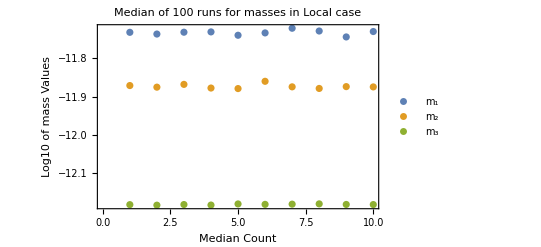

```mathematica
p1=ListPlot[Log10[{median1d,median2d,median3d}],Frame->True,PlotLegends->{Subscript[m, 1], Subscript[m, 2], Subscript[m, 3]},FrameLabel->{Style["Median Count",Black],Style["Log10 of mass Values",Black]},LabelStyle->Black,PlotLabel->"Median of 100 runs for masses in Local case"]
```

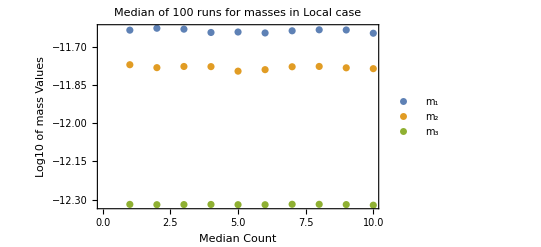

```mathematica
p2=ListPlot[Log10[{median1m,median2m,median3m}],Frame->True,PlotLegends->{Subscript[m, 1], Subscript[m, 2], Subscript[m, 3]},FrameLabel->{Style["Median Count",Black],Style["Log10 of mass Values",Black]},LabelStyle->Black,PlotLabel->"Median of 100 runs for masses in Local case"]
```

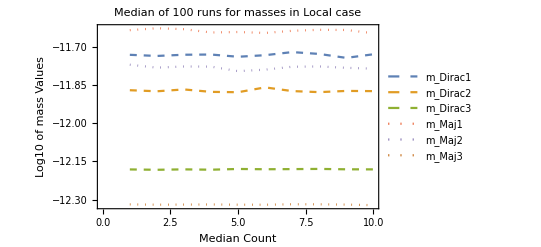

```mathematica
ListLinePlot[Log10[{median1d,median2d,median3d,median1m,median2m,median3m}],Frame->True,PlotStyle->{Directive[Dashed],Directive[Dashed],Directive[Dashed],Directive[Dotted],Directive[Dotted],Directive[Dotted]},FrameTicksStyle->Directive[Black,FontSize->15],PlotLegends->{Subscript[m,Dirac1],Subscript[m,Dirac2],Subscript[m,Dirac3],Subscript[m,Maj1],Subscript[m,Maj2],Subscript[m,Maj3]},FrameLabel->{Style["Median Count",Black,16],Style["Log10 of mass Values",Black,15]},LabelStyle->Black,PlotLabel->Style["Median of 100 runs for masses in Local case",15]]
```

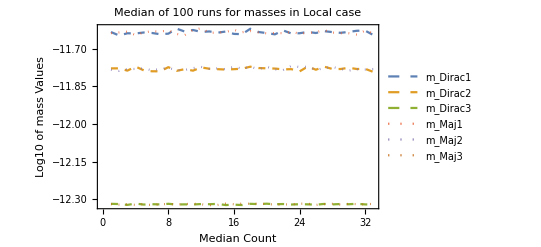

-Graphics-